# MATH 340: September 16 Class

## Some Practice with Basic Mathematica

1. Evaluate the following expressions first as an exact value, and then as a decimal value with at least 10 digits.

```mathematica
Sin[Pi/12]
```

(-1+√3)/(2 √2)

```mathematica
N[Sin[Pi/12],10]
```

0.2588190451

```mathematica
(15*E^3-7)^(1/2)
```

√(-7+15 ⅇ^3)

```mathematica
N[(15*E^3-7)^(1/2),10]
```

17.15468023

And so on for the rest of the problem 1 examples.

2. Generate graphs of the following functions.

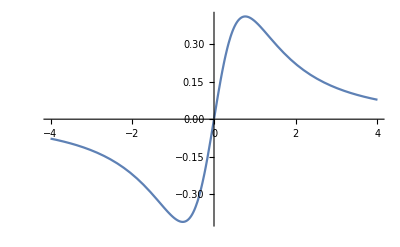

```mathematica
Plot[ArcTan[x]/(x^2+1),{x,-4,4}]
```

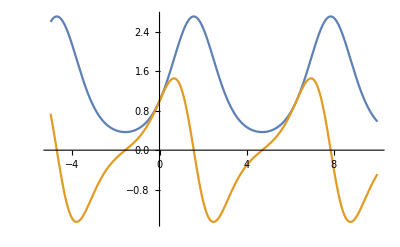

```mathematica
Plot[{Exp[Sin[x]],Cos[x]*Exp[Sin[x]]},{x,-5,10}]
```

```mathematica
Plot3D[Exp[-x^2-(y^2)],{x,-2,2},{y,-3,1}]
```

-Graphics3D-

3. Using ContourPlot

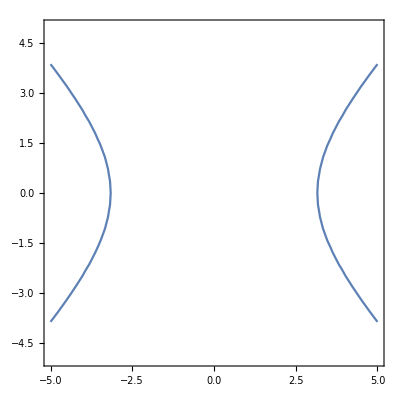

```mathematica
ContourPlot[(x^2)/5-(y^2)/5==2,{x,-5,5},{y,-5,5},Axes->True]
```

4. Using manipulate

```mathematica
Manipulate[ContourPlot[x^2/a^2+y^2/b^2==1,{x,-10,10},{y,-10,10}],{a,1,10},{b,1,10}]
```

## New Stuff for Today: Differential Equations

```mathematica
(* Solving DE's: IF an analytical solution exists 
Use DSolve[{system of DE's}, function, variable] *)
(* Example: dy/dt = y - sin(t);y(0)=3 *)
```

```mathematica
DSolve[{y'[t]==y[t]-Sin[t],y[0]==3},y[t],t]
```

{{y[t]→1/2 (5 ⅇ^t+Cos[t]+Sin[t])}}

```mathematica
(* no initial value *)
DSolve[{y'[t]==y[t]-Sin[t]},y[t],t]
```

{{y[t]→ⅇ^t C[1]+1/2 (Cos[t]+Sin[t])}}

```mathematica
(* system of DEs *)
DSolve[{x'[t]==y[t],y'[t]==x[t]-y[t]},{x[t],y[t]},t]
```

{{x[t]→1/10 ⅇ^(-t/2-(√5 t)/2) (5-√5+5 ⅇ^(√5 t)+√5 ⅇ^(√5 t)) C[1]+(ⅇ^(-t/2-(√5 t)/2) (-1+ⅇ^(√5 t)) C[2])/(√5),y[t]→(ⅇ^(-t/2-(√5 t)/2) (-1+ⅇ^(√5 t)) C[1])/(√5)-1/10 ⅇ^(-t/2-(√5 t)/2) (-5-√5-5 ⅇ^(√5 t)+√5 ⅇ^(√5 t)) C[2]}}

```mathematica
(* plotting sol'n *)
mysoln=DSolve[{x'[t]==y[t],y'[t]==x[t]-y[t],x[0]==2,y[0]==-1},{x[t],y[t]},t];
```

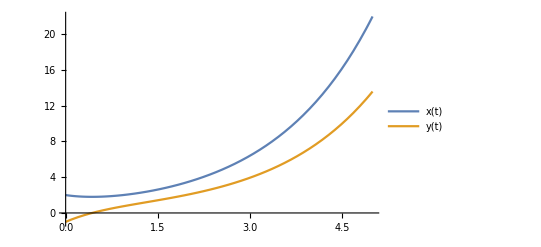

```mathematica
Plot[{x[t]/.mysoln,y[t]/.mysoln},{t,0,5},PlotLegends->{"x(t)","y(t)"}]
```

```mathematica
(* What if there is no nice analytic solution? *)
system={
f'[t]==-w[t]-f[t]^2,
f[0]==2,
w'[t]==2*f[t]-w[t]^3,
w[0]==2
};
```

```mathematica
DSolve[system,{f[t],w[t]},t]
```

$Aborted

```mathematica
solution=NDSolve[system,{f[t],w[t]},{t,0,20}]
```

{{f[t]→InterpolatingFunction[…][t],w[t]→InterpolatingFunction[…][t]}}

```mathematica
plotthese={
f[t]/.solution,
w[t]/.solution
};
```

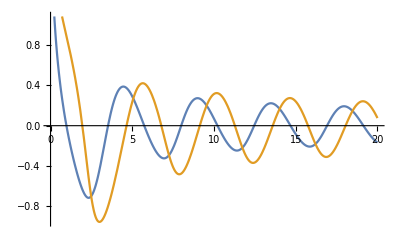

```mathematica
Plot[plotthese,{t,0,20}]
```

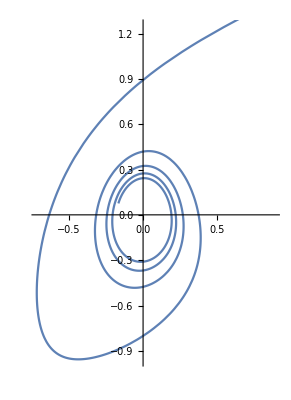

```mathematica
ParametricPlot[Evaluate[{f[t],w[t]}/.solution],{t,0,20}]
```